Keyhole modeling for the temperature field. This is some of the first trials for the simple source terms that include different point and line moving sources. The basics are explained inside the book “Keyhole Welding: The Solid and Liquid Phases” by Alexander Kaplan.

## Steady State 3d Solutions based on Moving Point Sources of Heat:

```mathematica
A = 0.4;  (*absorptance*)
PL = 150;  (*power*)
K = 20;   (* conductivity *)
κ =  10; (* thermal diffusivity *)
Ta = 298; (* ambient temperature *)
T[x_,y_,z_]:= Ta + 2 A PL/K Sqrt[x^2+y^2+z^2]Exp[-v[x+Sqrt[x^2+y^2+z^2]]/(2 κ)]
```

Rosenthal solution for the line source model

The solution for the temperature field T(r,ϕ) in the polar coordinates is given by the analytical solution:
T(r,ϕ) = T_a+P'/2 πλ_th K_o(Pe *r) exp(-Pe * r *cos(ϕ)) where Pe is modified Peclet number:
Pe = ⋁/2κ, T_a - ambient temperature, λ_th is the thermal diffusivity, K_0() is the modified Bessel function
of second kind and zeroth order. The temperature has a singularity at the origin, where the line source
with power per unit depth P is located.
The previous equation can be calculated to explicitly give the strength P’ which is necessary to reach evaporation of the arbitrary point in polar coordinates. 
P’(r,ϕ) = (T_v-T_a) 2 πλ_th 1/(K_o(Pe * r))exp(Pe * r cos(ϕ))

The heat flow is determined by Fourier’s law of heat conduction that can be simplified by considering only of the radial component:
q = -λ_th ∇T = -λ_th(∂T)/(∂r)
Spatial derivation of the temperature of the Rosenthal solution with respect to r leads to:
∂T/∂r = P' (r, ϕ)/(2 πλ_th)Pe'[-K_0(Pe' r) cos(ϕ) + (K')_0(Pe*r)]exp(-Pe r cos(ϕ))
K'_o(x) = -K_1(x)
q(r,ϕ) = -λ_th∂T/∂r = P’(r,ϕ)/2π Pe'(K_0(Pe'r) cos(ϕ) + K_1(Pe'r)) exp(-Pe'r cos(ϕ))

If we consider the boundary condition that the evaporation temperature Tv shall be reached at 
keyhole wall.
q_v(r,ϕ) = (T_v-T_a)λ_th Pe'(cos(ϕ)+K_1(Pe'r)/K_0(Pe'r))
Keyhole profile in the x-z plane only the azimuthal angle ϕ=0,π are of interest, describing the heat
loses of any point xf at the front wall (ϕ=0)
q_v(x_r)=(T_v-T_a)λ_th Pe'(-1 + K_1(Pe’ x_r)/K_0(Pe’ x_r))

```mathematica
Pe = v/(2κ);
qvf[xf_]:= (Tv-Ta)λ Pe (-1+BesselK[1,Pe * xf])/BesselK[0,Pe xf];
qvr[xr_] := (Tv-Ta)λ Pe (1+BesselK[1, Pe * xr]) /BesselK[0, Pe xr];
```

The intensity of the laser beam with only Fresnel absorption:

```mathematica
I0=2 PL/(rf0^2 π);
Intensity[x_,z_]:= I0 * (rf/rf0)^2 Exp[-2 r^2/rf^2];
rf0 = 2 F*M^2/π;
```

Beam radius is varying over the depth by:

```mathematica
zr = 2 rf0 *F;
rf[z_]:= rf0(1+((z-z0)/zr)^2)^(1/2)
```

According the figure local energy balance at the keyhole wall is given by:
tan(θ_w) = q_v/I_a=f(x,z)
which we will give angle θ_w. I_ais the intensity at the wall.

For further absorption we will have additional plasma absorption due to Bremsstralung and
Fresnel absorption during multiple reflections Iamr:

```mathematica
tanθw =( qv[x,z]-IaiB[x,z]-Iamr[x,z] )/IaFr[θw];
```

## Algorithm for the calculation

For every z_i at keyhole wall calculate downwards for both walls:
	Calculate new x (r) coordinate from the previous step.
	For every slice calculate the location of the moving line source (which is different than beam axis)
	   Distance x_fand x_r decide about the  position of the line source x_0to satisfy the general equation for the qv flow.
	   Calculate the new θ_w from  the absorbed power to the laser intensity Ia.
	   The algorithm is finished when back and front wall start cross. 

This calculation should be done two times. The first time only with I_a  we get the first description of the keyhole. The second run then estimate different absorption mechanisms and yields the final keyhole profile.

```mathematica
Clear[x];
```

```mathematica
rf0 = 2*1064 10^-6 F M^2/π
```

0.0203209

```mathematica
(* laser power *)
I0=2 PL/(rf0^2 π);
rf0 =2 wave F M^2/π;
(* absorption by the vapour plume / damping by plasma plume *)
Subscript[α, pl] = 1-Exp[-Subscript[α, iB] * Subscript[h, pl]];
(* the first run plasma absorption by Bremsstralung *)
Subscript[α, iB1] = 1-Exp[-Subscript[α, iB]d/2];
(*partial absorption of the intensity*)
Subscript[α, iBmr]=1-Exp[-Subscript[α, iB] 3d/2];

(* incident intensity *)
zr = 2 rf0 *F;
rf[z_]:= rf0(1+((z-z0)/zr)^2)^(1/2);

Ia[x_,z_]:= I0 * (rf[z]/rf0)^2 Exp[-2 x^2/rf[z]^2];
(* different contributions to the absorption *)
IaFr[x_,z_]:= (1-Subscript[α, pl])(1-Subscript[α, iB1])*Subscript[α, Fr] *Ia[x,z];
Iamr[x_,z_]:= (1-Subscript[α, pl])(1-Subscript[α, iB1])*(1-Subscript[α, Fr])Subscript[α, mr] *Ia[x,z];
IaiB[x_,z_]:= (1-Subscript[α, pl])(Subscript[α, iB1]+Subscript[α, iBmr] *(1-Subscript[α, iB1])(1-Subscript[α, Fr])(1-Subscript[α, mr]) )*Ia[x,z];
Ir[x_,z_]:= (1-Subscript[α, pl])(1-Subscript[α, iB1])*(1-Subscript[α, Fr])(1-Subscript[α, mr])(1-Subscript[α, iBmr])*Ia[x,z];

calculateAbsorption[x_,z_, power_]:= Module[{I0 = 2 power/(rf0^2 π)},
zr = 2 rf0 *F;
rf[z]:= rf0(1+((z-z0)/zr)^2)^(1/2);
Ia[x,z]:= I0 * (rf[z]/rf0)^2 Exp[-2 x^2/rf[z]^2];
(*Ia[x,z]:= I0 * Exp[-2 x^2/rf[z]^2];*)
IaFr[x,z]:= (1-Subscript[α, pl])(1-Subscript[α, iB1])*Subscript[α, Fr] *Ia[x,z];
IaFr[x,z]
];

Pe = v/(2κ);
qvf[xf_]:= (Tv-Ta)λ Pe (1+BesselK[1,Pe * xf])/BesselK[0,Pe xf];
qvr[xr_] := (Tv-Ta)λ Pe (-1+BesselK[1, Pe * xr]) /BesselK[0, Pe xr];
(* this are simplified versions of the above functions *)
qvcr[rkh_]:= (Tv-Ta)λ κ/2 (v * rkh/(2 κ))^-0.7;
qvcf[rkh_]:= (Tv-Ta) λ κ/2  (2+(v * rkh/(2 κ))^-0.7);
findRearAndFront[v_, κ_, Ta_,Tv_, 𝒜_, pow_,xk_List, off_,d_,λ_]:= Module[{xrstart=-2, xfstart=(xk[[1]]+xk[[2]]) / 2
, xfmin=xk[[1]], xfmax =xk[[2]],r,θ},
Tn[r_,θ_]:=Ta + (𝒜 pow)/(2π λ d)Exp[-v r Cos[θ]/(2 κ)] BesselK[0,v* r/(2 κ)];
Print[pow, off, xk];
(* find point where temperature is Tv *)
xr=FindRoot[Tn[Abs[x-off],π]==Tv, {x,-5,-0.01}];
xf=FindRoot[Tn[x-off,0]== Tv, {x,xfmin,xfmax}];
{Re[x/.xr],Re[x/.xf]}
];
Clear[findPower];
findPower[v_, κ_, xk_List,Ta_,Tv_,𝒜_,d_,λ_]:= Module[{xr=xk[[1]],xf=xk[[2]],x0},
Pl[r_,θ_]:=(Tv-Ta)2π λ  d/𝒜 1/BesselK[0, v r/(2κ)] Exp[v r Cos[θ]/(2κ)];
fr=FindRoot[Pl[Abs[xr-x0],π]==Pl[xf-x0,0],{x0,xr,xf}];
{Re[Pl[xf-x0/.fr,0]], Re[x0/.fr]}]
```

```mathematica
rf0
```

2.02445

```mathematica
Pe
```

1.32979

```mathematica
x1={-0.5511059201951887,-0.004411116479318331};p1=2660.3611639948417;off1=-0.11137274624218212;
```

```mathematica
xl =findRearAndFront[v,κ, Ta,Tv,Subscript[α, Fr],4000,{-3,1},off1, d, λ]
```

4000-0.111373{-3,1}

{-0.182676,-0.0647574}

```mathematica
calculateAbsorption[2.2,2, 4000]
```

4.16879×10^-76

```mathematica
findPower[v,κ,xl, Ta,Tv,Subscript[α, Fr],d, λ]
```

{2660.36,-0.111373}

```mathematica
qv = {qvr[Abs[#1]], qvf[#2]}& @@ xl
```

{424.901,-157.033-245.33 ⅈ}

```mathematica
Ia[#,0]& /@ xl
```

{61764.6,61764.6}

```mathematica
IaFr[Abs[#],0]& /@ xl
```

{19623.6,19623.6}

```mathematica
θ = π/2; δz = 0.02; 𝒳={}; 𝒵={}; 𝒪={}; 𝒫={};
(* initialize parameters *)
power=PL; offset = 0; eps=10^-3; xkh={-2,0.5};
xkh = findRearAndFront[v,κ,Ta,Tv, Subscript[α, Fr],power, xkh, offset, d, λ];
rkh = xkh[[2]]-xkh[[1]];
For[z=0, z <3d, z = z+δz,
(*xkh = findRearAndFront[v,κ,Ta,Tv, Subscript[α, Fr],power, xkh, offset, d, λ];*)
(* calculation of the reflection with average angle θ *)
Subscript[ρ, mr]= Subscript[ρ, Fr]^(π/(4θ)-1);
Subscript[α, mr] = 1-Subscript[ρ, mr];
(* calculate the shape of keyhole, the heat losses *)
qv = {qvcr[Abs[rkh]], qvcf[rkh]};

(* tanθw =( qv-IaiB[x,z]-Iamr[x,z] )/IaFr[x,z]; *)
Ifrens=calculateAbsorption[Abs[#],z, power]&/@ xkh;

(*Ic = (IaiB[#,z]+Iamr[#,z])& /@ xkh;*)
tanθw = qv/Ifrens;
If[MatchQ[Ifrens,_Complex]|| MatchQ[qv,_Complex],Break[]];
xkh = xkh - δz*Re[tanθw];(*  Print["New:",xkh,{offset,power}]; *)
rkh = xkh[[2]]-xkh[[1]];
(*{power, offset} =findPower[v,κ, xkh, Ta, Tv, Subscript[α, Fr],d, λ];*)
θ = ArcTan[tanθw]; AppendTo[𝒳,xkh]; AppendTo[𝒵,z]; AppendTo[𝒪,offset];AppendTo[𝒫,power];
(* curvature of keyhole closes *) 
If[ xkh[[1]]>xkh[[2]],Break[] ];]
```

40000{-2,0.5}

General::munfl: Exp[-3.25436×10^7] is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

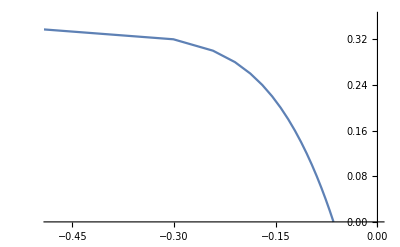

```mathematica
rear=ListLinePlot[Partition[Riffle[𝒳[[All,1]],𝒵],2]]
```

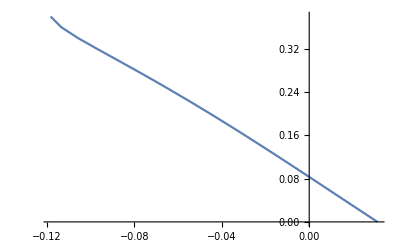

```mathematica
front=ListLinePlot[Partition[Riffle[𝒳[[All,2]],𝒵],2] ]
```

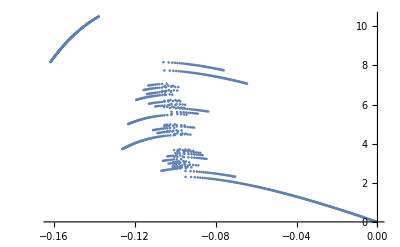

```mathematica
ListPlot[Partition[Riffle[𝒪,𝒵],2] ]
```

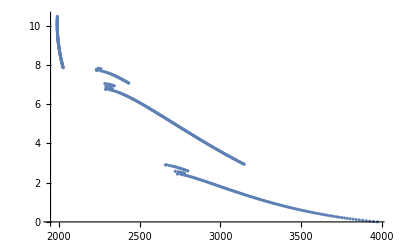

```mathematica
ListPlot[Partition[Riffle[𝒫,𝒵],2] ]
```

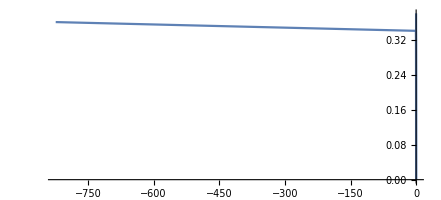

```mathematica
Show[{rear,front},PlotRange->"Full", AspectRatio->True]
```

```mathematica
Last[𝒳]
```

{-1.68007,0.224743}

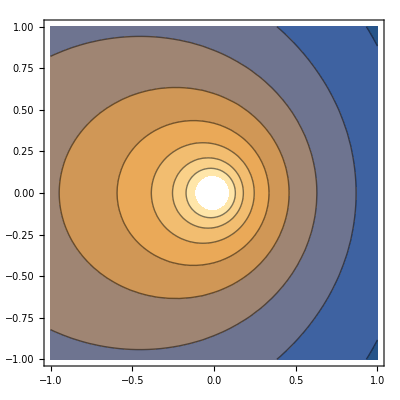

```mathematica
Tn[x_,y_,P_,dis_]:=Ta + P/(2π λ dis)Exp[-v x / (2 κ)] BesselK[0,v* Norm[{x,y}]/(2 κ)];
ContourPlot[Tn[x,y,2450,3.], {x,-1,1},{y,-1,1}, AspectRatio->True]
```

```mathematica
FindRoot[Tn[x,0] == Tv, {x,-4}]
```

{x→-2.16526}

```mathematica
T[r,π]/.%151
```

3173.

```mathematica
(2 PL)/(π rf0^2)
```

(π PL)/(2 F^2 M^4)

```mathematica
(π PL)/(2 F^2 M^4)
```

(π PL)/(2 F^2 M^4)

```mathematica
qvr[0.8]
```

689.283

## Absorption

The plasma absorption can be described by Beer-Lambert law:
I_a(z)/I_i(0) = 1-I_t(z)/I_i(0)=1-exp(-α_iB z)
where I_i -is the incident intensity, I_t-the transmitted intensity and I_a is the intensity absorbed when passing path z. For the plasma absorption coefficient due to
inverse Bremsstrahlung α_iB that is temperature dependent. Mean value of 100 m^-1 is used.
Absorbed fraction of the metal vapour plume over the workpiece is known by estimating height
h_pl of the plume : 
α_pl=1-exp(-α_iB h_pl)
The remaining radiation  is transmitted and passes the plume. The power hitting the workpiece outside
the keyhole is strongly reflected and only small part is absorbed. The first plasma absorption before
hitting the keyhole wall:
α_(iB,1)= 1-exp(-α_iBd/2)
The first Fresnel absorption at each point is included in the energy balance by multiplying the local beam intensity by the Fresnel absorption coefficient.
After n_mr reflections, assuming geometrical optics, the part of the remaining intensity I_rn:
I_rn/I_i=(ρ_Fr)^nmr
where ρ_Fr is  the Fresnel reflection coefficient, which is in general angle-dependent.
The approximation of the keyhole profile with mean wall angle θ_w the angle of reflection θ_r=2 n_mr θ_w

The number of the reflections is defined by counting them up to the limiting angle of the reflected beam:
θ_r≥π/2..
n_mr=(π/2)/(2 θ_w)=π/(4 θ_w)
If the first reflection, which is separately considered in the energy balance.
Using previous equation for the number of reflections:
ρ_mr=[ρ_Fr(θ=π/2)]^(nmr-1)
Consequently the absorption coefficient α_mr:
α_mr=1-ρ_mr

During the reflections the rays cross plasma and are partially absorbed by it. 
α_(iB,mr)=1-exp(-α_iB3d/2)

The of the incident intensities damped by the plume minus the remaining intensity I_r leaving the
keyhole:
I_(a,Fr)+I_(a,mr)+I_(a,iB)=(1-α_pl)I(x,z)-I_r=f(θ_w) 
where:
I_r=(1-α_pl)(1-α_(iB,1))(1-α_Fr) x(1-α_mr)(1-α_(iB,mr))I(x,z)

I_(a,Fr)=(1-α_pl)*(1-α_(iB,1))α_Fr I(x,z)
I_(a,mr)=(1-α_pl)*(1-α_(iB,1))(1-α_Fr)α_mrI(x,z)
I_(a,iB)=(1-α_pl)(α_(iB,1)+α_(iB,mr)(1-α_(iB,1))x(1-α_Fr)(1-α_mr)) I(x,z)

```mathematica
Subscript[α, pl] = 1-Exp[-Subscript[α, iB] * Subscript[h, pl]];
nmr = π/(4 θw);
```

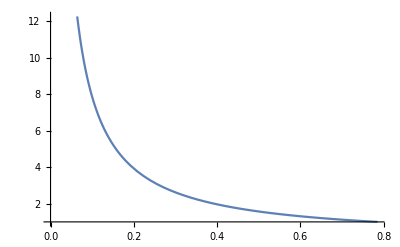

```mathematica
Plot[π/(4 θ), {θ,0,π/4}]
```

General::munfl: 0.8^48950. is too small to represent as a normalized machine number; precision may be lost.

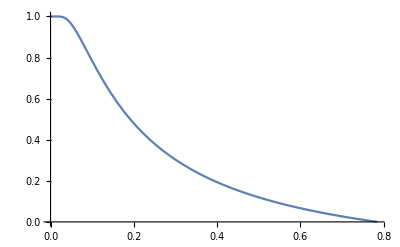

```mathematica
With[{ρ=0.8},Plot[1-ρ^(π/(4θ)-1), {θ,0,π/4}]]
```

Reflections from the keyhole, the first reflection is calculated separately in the energy balance. The rest reflections
can be approximated from the multiple reflections:

```mathematica
ρmr = ρFr^(nmr-1);
αmr = 1-ρmr;
```

This effect of the partial absorption of the intensity  can be modeled:

```mathematica
Subscript[α, iBmr]=1-Exp[-Subscript[α, iB] 3d/2];
```

After the first iteration of the algorithm we calculate the absorptions using the next sequence:

```mathematica
IaFr[x_,z_]:= (1-Subscript[α, pl])(1-Subscript[α, iB1])*Subscript[α, mr] *Ia[x,z];
Iamr[x_,z_]:= (1-Subscript[α, pl])(1-Subscript[α, iB1])*(1-Subscript[α, Fr])Subscript[α, mr] *Ia[x,z];
IaiB[x_,z_]:= (1-Subscript[α, pl])(Subscript[α, iB1]+Subscript[α, iBmr] *(1-Subscript[α, iB1])(1-Subscript[α, Fr])(1-Subscript[α, mr]) )*Ia[x,z];
Ir[x_,z_]:= (1-Subscript[α, pl])(1-Subscript[α, iB1])*(1-Subscript[α, Fr])(1-Subscript[α, mr])(1-Subscript[α, iBmr])*Ia[x,z];
```

Parameters used in the calculation:
Laser power (cw)  Pl  4kW
Wavelength             λ   10.6   μm
Polarisation            -    unpolarized -
Beam quality          M^2   5.0
Beam mode          TEM  TEM_00
Focal length          f         200    mm
Beam diameter on optics  D_b     34
Focusing number     F = f / D_b       6.0
Focal radius               r_f0       203 , μm
Rayleigh length        z_r      2.5    mm
Absorption coefficient Bremsstrahlung    α_iB  100 m^-1
Focal plane                 z_0    optimized 0.7
welding speed           v        50  mm/s
Initial depth of keyhole  d    3.5 mm
Material                      mild steel
	λ                          45 W/mK
	κ                          18.8 mm^2/s
Weld                             blind weld

```mathematica
PL = 4 10^3;
M = Sqrt[5];
F = 6.0;
wave =10.6 10^-3;
rf0 = 0.203;
zr = 2.5;
z0 = 0.7;
v = 60.0;
Subscript[α, iB]= 100 10^-3;
Subscript[h, pl] = 0.8;
d =5.5;
(* this is the function of the incident angle *)
Subscript[α, Fr] = 0.41;  
Subscript[ρ, Fr]=1-Subscript[α, Fr];
Ta = 298;
Tv = 2900+273;
κ = 18.8; λ= 45*10^-3;
```

```mathematica
Gaseous phase
```

The state of the vapour inside the keyhole is calculated for each element after having calculate the keyhole profile.

The degree of ionization as a function of temperature is Saha’s equation:
n_en_i/n_n = 2(g_o)_i/g_n (2πmkT)/h^3exp(-W_i/kT)
where n_e,n_i and n_n are the particle densities of electrons, ions and ground state atoms respectively and g_0 is the statistical weight. The electron mass m_e, Planck’s constant ℏ = h/2π and Boltzmann constant k.
W_i denotes the work for ionization.

The dominant absorption mechanism in a plasma for CO2 laser radiation is the mechanism of inverse Bremsstrahlung.  Linear plasma absorption coefficient α_iB:

α_iB= (Z^2 e^6 n_e)/(6 √3 ℏω^3 m_e^2 c_0 ϵ_0^3(1-(ω_pe/ω)^2)) x(m/(2πkT))(1-exp(-ℏω/kT))ḡ